1.

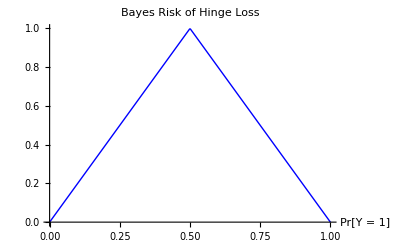

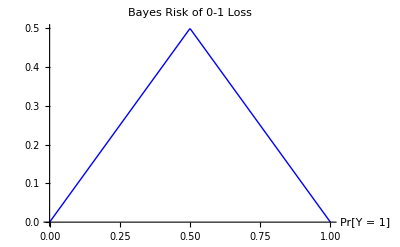

```mathematica
hinge[r_, y_] := Max[1 - r y, 0]
logistic[r_,y_] := Log[1 + Exp[- r y]]
ex[L_,r_, p_] := p L[r,1] + (1-p) L[r,-1]
Risk[L_, p_] := Minimize[ex[L,r,p], {r}][[1]]
Risk[hinge, 0.5]
Plot[Risk[hinge,p], {p,0,1}, PlotLabel-> "Bayes Risk of Hinge Loss" ,  AxesLabel->{"Pr[Y = 1]"}, PlotStyle->{Blue, Thick}]
Plot[0.5 Risk[hinge,p], {p,0,1}, PlotLabel-> "Bayes Risk of 0-1 Loss" ,  AxesLabel->{"Pr[Y = 1]"}, PlotStyle->{Blue, Thick}]
Plot[Risk[logistic,p], {p,0,1},  PlotLabel-> "Bayes Risk of Logistic Loss", AxesLabel->{"Pr[Y = 1]"}, PlotStyle->{Blue, Thick}  ]
```